Лабораторная работа №2

Дано: P={p_1(x_1,y_1), p_2(x_2,y_2),..., p_n(x_n,y_n)} – простой многоугольник;
p_0(x_0,y_0) – точка

Надо: Используя “лучевой тест” определить положение точки p_0 относительно многоугольника P.

Примечания: в качестве результата выдается сообщение и картинка с изображением точки и многоугольника с подписанными вершинами. Первым этапом реализовать “габаритный тест”.
В случае попадания луча в вершину многоугольника обрабатывать эту ситуацию (не генерировать новый луч).

Решение:

Точка лежит в многоугольнике

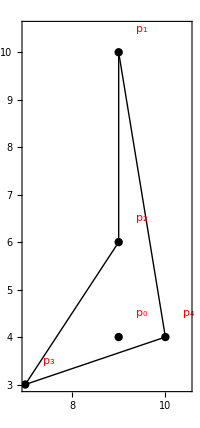

```mathematica
countIntersects[P_,p0_,q_]:=(
counter=0;(*счетчик пересечений луча p0q и сторон многоугольника P*)
isRepeat=True;(*показатель повторяемости точки пересечения вершины многоугольника с лучом*)
isRepeatTbl=Table[True,{k,1,Length[P]}];
For[i=1,i<=Length[P],i++,
iN=Mod[i,Length[P]]+1;(*i Next - индекс, следующий за текущим i*)
iP=If[i==1,Length[P],i-1];(*i Previous - индекс, идущий перед текущим i*)
Subscript[d, 1]=Det[({{p0[[1]]-P[[i]][[1]], p0[[2]]-P[[i]][[2]]}, {P[[iN]][[1]]-P[[i]][[1]], P[[iN]][[2]]-P[[i]][[2]]}})];
Subscript[d, 2]=Det[({{q[[1]]-P[[i]][[1]], q[[2]]-P[[i]][[2]]}, {P[[iN]][[1]]-P[[i]][[1]], P[[iN]][[2]]-P[[i]][[2]]}})];
Subscript[d, 3]=Det[({{P[[i]][[1]]-p0[[1]], P[[i]][[2]]-p0[[2]]}, {q[[1]]-p0[[1]], q[[2]]-p0[[2]]}})];
Subscript[d, 4]=Det[({{P[[iN]][[1]]-p0[[1]], P[[iN]][[2]]-p0[[2]]}, {q[[1]]-p0[[1]], q[[2]]-p0[[2]]}})];
Subscript[v, 1]=(p0-P[[i]]).(p0-P[[iN]]);
Subscript[v, 2]=(q-P[[i]]).(q-P[[iN]]);
Subscript[v, 3]=(P[[i]]-p0).(P[[i]]-q);
Subscript[v, 4]=(P[[iN]]-p0).(P[[iN]]-q);
If[(Subscript[d, 1]==0&&Subscript[d, 2]==0&&Subscript[d, 3]==0&&Subscript[d, 4]==0&&(Subscript[v, 1]≤0||Subscript[v, 2]≤0||Subscript[v, 3]≤0||Subscript[v, 4]≤0))||(Subscript[d, 1]*Subscript[d, 2]≤0&&Subscript[d, 3]*Subscript[d, 4]≤0),
counter++;
xN=(P[[iN]][[1]]-P[[i]][[1]])*(P[[iP]][[1]]-P[[i]][[1]]);(*статус соседних вершин относительно текущей по оси Ox*)
yN=(P[[iN]][[2]]-P[[i]][[2]])*(P[[iP]][[2]]-P[[i]][[2]]);(*статус соседних вершин относительно текущей по оси Oy*)
If[P[[i]][[1]]==p0[[1]]&&p0[[1]]==q[[1]],
If[isRepeatTbl[[i]]==True&&xN<=0,{isRepeatTbl[[i]]=False;counter--;},isRepeatTbl[[i]]=True];
];
If[P[[i]][[2]]==p0[[2]]&&p0[[2]]==q[[2]],
If[isRepeatTbl[[i]]==True&&yN<=0,{isRepeatTbl[[i]]=False;counter--;},isRepeatTbl[[i]]=True];
];
]
];
If[IntersectingQ[{p0},P],counter=1];
Return[counter]
)
(*лежит ли точка р в отрезке а1а2*)
isIn[p_,a1_,a2_]:=(
If[p≤a2&&p≥a1,Return[True],Return[False]]
)
isSimple=False;(*простой ли многоугольник*)
While[isSimple==False,
isSimple=True;
n=RandomChoice[Range[3,10]];
Do[{Subscript[x, k]=RandomChoice[Range[10]],Subscript[y, k]=RandomChoice[Range[10]],Subscript[p, k]={Subscript[x, k],Subscript[y, k]}},{k,1,n}];
For[i=1,i+2≤n,i++,
For[j=i+2,j≤n&&j-i≤n-2,j++,
If[Det[({{Subscript[x, i]-Subscript[x, j], Subscript[y, i]-Subscript[y, j]}, {Subscript[x, Mod[j,n]+1]-Subscript[x, j], Subscript[y, Mod[j,n]+1]-Subscript[y, j]}})]*Det[({{Subscript[x, i+1]-Subscript[x, j], Subscript[y, i+1]-Subscript[y, j]}, {Subscript[x, Mod[j,n]+1]-Subscript[x, j], Subscript[y, Mod[j,n]+1]-Subscript[y, j]}})]≤0&&Det[({{Subscript[x, j]-Subscript[x, i], Subscript[y, j]-Subscript[y, i]}, {Subscript[x, i+1]-Subscript[x, i], Subscript[y, i+1]-Subscript[y, i]}})]*Det[({{Subscript[x, Mod[j,n]+1]-Subscript[x, i], Subscript[y, Mod[j,n]+1]-Subscript[y, i]}, {Subscript[x, i+1]-Subscript[x, i], Subscript[y, i+1]-Subscript[y, i]}})]≤0,{isSimple=False,Break[]},]
];
If[isSimple==False,Break[]]
]
]
(*
n;
Table[Subscript[p, k],{k,1,n}];
*)
(*Тестирование заданных многоугольников [Ввести все!]*)
(*
n=5;
{Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5]}={{3,1},{7,5},{8,9},{8,10},{7,10}};
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]},{Subscript[x, 5],Subscript[y, 5]}}={{3,1},{7,5},{8,9},{8,10},{7,10}};
Table[Subscript[p, k],{k,1,n}];
*)
(*
n=4;
{Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4]}={{9,10},{9,6},{7,3},{10,4}};
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]}}={{9,10},{9,6},{7,3},{10,4}};
Table[Subscript[p, k],{k,1,n}];
*)

Subscript[x, 0]=RandomChoice[Range[10]];
Subscript[y, 0]=RandomChoice[Range[10]];
Subscript[p, 0]={Subscript[x, 0],Subscript[y, 0]};
(*Габаритный тест*)
Subscript[x, min]=Subscript[x, 1];
Subscript[y, min]=Subscript[y, 1];
Subscript[x, max]=Subscript[x, 1];
Subscript[y, max]=Subscript[y, 1];
For[i=1,i≤n,i++,
If[Subscript[x, min]>Subscript[x, i],Subscript[x, min]=Subscript[x, i]];
If[Subscript[x, max]<Subscript[x, i],Subscript[x, max]=Subscript[x, i]];
If[Subscript[y, min]>Subscript[y, i],Subscript[y, min]=Subscript[y, i]];
If[Subscript[y, max]<Subscript[y, i],Subscript[y, max]=Subscript[y, i]];
]
(*Завершение габаритного теста*)

(*Тестирование заданных точек*)

xxx=9;
yyy=4;
Subscript[p, 0]={xxx,yyy};
{Subscript[x, 0],Subscript[y, 0]}={xxx,yyy};


If[Subscript[x, min]>Subscript[x, 0]||Subscript[x, 0]>Subscript[x, max]||Subscript[y, min]>Subscript[y, 0]||Subscript[y, 0]>Subscript[y, max],"Точка не лежит в многоугольнике",
If[isIn[Subscript[x, 0],Subscript[x, min],Subscript[x, max]],
If[Subscript[y, 0]<Subscript[y, max],
If[Mod[countIntersects[Table[Subscript[p, k],{k,1,n}],Subscript[p, 0],{Subscript[x, 0],Subscript[y, max]+10}],2]==0,
"Точка не лежит в многоугольнике","Точка лежит в многоугольнике"],
If[Mod[countIntersects[Table[Subscript[p, k],{k,1,n}],Subscript[p, 0],{Subscript[x, 0],Subscript[y, min]-10}],2]==0,
"Точка не лежит в многоугольнике","Точка лежит в многоугольнике"]
],
If[Subscript[x, 0]<Subscript[x, max],
If[Mod[countIntersects[Table[Subscript[p, k],{k,1,n}],Subscript[p, 0],{Subscript[x, max]+10,Subscript[y, 0]}],2]==0,
"Точка не лежит в многоугольнике","Точка лежит в многоугольнике"],
If[Mod[countIntersects[Table[Subscript[p, k],{k,1,n}],Subscript[p, 0],{Subscript[x, min]-10,Subscript[y, 0]}],2]==0,
"Точка не лежит в многоугольнике","Точка лежит в многоугольнике"]
]
]
]

Subscript[p, 0]={Subscript[x, 0],Subscript[y, 0]};
Show[Graphics[{PointSize[0.015],Thick,Black,Table[Line[{Subscript[p, k],Subscript[p, Mod[k,n]+1]}],{k,1,n}],Table[Text[Style[Subscript["p", k],Red],{Subscript[x, k]+0.5,Subscript[y, k]+0.5}],{k,0,n}],PlotLabel->info,Point[Table[Subscript[p, k],{k,0,n}]]},PlotRange->{{15,-5},{15,-5}},Frame->True]]
```

```mathematica
counter
```

2

```mathematica
Table[Subscript[p, k],{k,1,n}]
```

{{9,10},{9,6},{7,3},{10,4}}